# Eigenvalues

## Basic Examples

Machine-precision numerical eigenvalues:

```mathematica
Eigenvalues[Table[N[1/(i+j+1)],{i,3},{j,3}]]
```

{0.657051,0.0189263,0.000212737}

```mathematica
Eigenvalues[HilbertMatrix[3]]
```

{Root1.41Root[-1+381 #1-3312 #1^2+2160 #1^3&,3]1.408318927123654,Root0.122Root[-1+381 #1-3312 #1^2+2160 #1^3&,2]0.12232706585390585,Root2.69 × 10^-3Root[-1+381 #1-3312 #1^2+2160 #1^3&,1]0.0026873403557735294}

Approximate 20-digit precision eigenvalues:

```mathematica
Eigensystem[Table[N[1/(i+j+1),20],{i,3},{j,3}]]
```

{{0.65705142829757924544,0.018926310974070914307,0.00021273691882603073422},{{0.70315285756764558448,0.54926761436970279528,0.45153199964019137174},{0.66853480067837342014,-0.29444000664816214587,-0.68291017181394930029},{0.24215135592513588838,-0.78205509415235298415,0.57424084714862671077}}}

Exact eigenvalues:

```mathematica
Eigenvalues[Table[1/(i+j+1),{i,2},{j,2}]]
```

{1/60 (16+√241),1/60 (16-√241)}

Symbolic eigenvalues:

```mathematica
Eigenvalues[{{a,b},{c,d}}]
```

{1/2 (a+d-√(a^2+4 b c-2 a d+d^2)),1/2 (a+d+√(a^2+4 b c-2 a d+d^2))}

## Options

### Cubics

Eigenvalues uses Root to compute eigenvalues:

```mathematica
Eigenvalues[{{1,2,0},{5,1,2},{6,7,1}}]
```

{Root6.34Root[-1-21 #1-3 #1^2+#1^3&,3]6.338158176564577,Root-3.29Root[-1-21 #1-3 #1^2+#1^3&,1]-3.290205382400845,Root-0.0480Root[-1-21 #1-3 #1^2+#1^3&,2]-0.04795279416373193}

Explicitly use the cubic formula to get the result in terms of radicals:

```mathematica
Eigenvalues[{{1,2,0},{5,1,2},{6,7,1}},Cubics->True]
```

{1+4/(1/2 (3+ⅈ √23))^(1/3)+2^(2/3) (3+ⅈ √23)^(1/3),1-(2 (1+ⅈ √3))/(1/2 (3+ⅈ √23))^(1/3)-(1-ⅈ √3) (1/2 (3+ⅈ √23))^(1/3),1-(2 (1-ⅈ √3))/(1/2 (3+ⅈ √23))^(1/3)-(1+ⅈ √3) (1/2 (3+ⅈ √23))^(1/3)}

### Method

```mathematica
d=DiagonalMatrix[{1,0.8+0.8ⅈ,ⅈ}];
```

```mathematica
t={{1,2,0},{0,3,2},{1,0,4}};
```

```mathematica
m=t.d.Inverse[t]
```

{{0.95+0.2 ⅈ,-0.1+0.4 ⅈ,0.05-0.2 ⅈ},{0.3-0.075 ⅈ,0.6+0.85 ⅈ,-0.3+0.075 ⅈ},{0.75-0.75 ⅈ,-0.5+0.5 ⅈ,0.25+0.75 ⅈ}}

By default, “Criteria”→”Magnitude” selects a largest-magnitude eigenvalue:

```mathematica
Eigenvalues[m,1,Method->"Arnoldi"]
```

{0.8+0.8 ⅈ}

Find the largest real-part eigenvalues:

```mathematica
Eigenvalues[m,1,Method->{"Arnoldi","Criteria"->"RealPart"}]//Chop
```

{1.}

Find the largest imaginary-part eigenvalues:

```mathematica
Eigenvalues[m,1,Method->{"Arnoldi","Criteria"->"RealPart"}]//Chop
```

{1.}

Find the largest imaginary-part eigenvalue:

```mathematica
Eigenvalues[m,1,Method->{"Arnoldi","Criteria"->"ImaginaryPart"}]//Chop
```

{0.+1. ⅈ}

Find two eigenvalues from both ends of the matrix spectrum:

```mathematica
d=DiagonalMatrix[{1,0.8,-1,2}];
t=Orthogonalize[{{1,2,0,1},{0,3,2,-2},{1,0,4,-1},{0,1,0,1}}];
m=t.d.Transpose[t];
```

```mathematica
Eigenvalues[m,2,Method->{"Arnoldi","Criteria"->"BothEnds"}]
```

{2.,-1.}

Use “StartingVector” to avoid randomness:

```mathematica
d=DiagonalMatrix[{1,-1,0.}];
t={{1,2,0},{0,3,2},{1,0,4}};
m=t.d.Inverse[t];
```

Different starting vectors may converge to different eigenvalues:

```mathematica
Eigenvalues[m,1,Method->{"Arnoldi","StartingVector"->{1,0,0}}]
```

{-1.}

```mathematica
Eigenvalues[m,1,Method->{"Arnoldi","StartingVector"->{0,0,1}}]
```

{1.}

Use “Shift”→μ to shift the eigenvalues by transforming the matrix m to m-ⅈ u. This preserves the eigenvectors but changes the eigenvalues by -μ. The method compensatest for the changed eigenvalues. “Shift” is typicallly used to find eigenpairs where there is no criteria such as largest or smallest magnitude that can select them:

```mathematica
d=DiagonalMatrix[{1,2,3}];
t={{1,2,0},{0,3,2},{1,0,4}};
m =N@t.d.Inverse[t];
```

```mathematica
μ=2.1;
```

Manually shift the matrix and adjust the resulting eigenvalue:

```mathematica
λl1=Eigenvalues[m-μ IdentityMatrix[3],-1,Method->"Arnoldi"]
```

{-0.1}

```mathematica
λl1=λl1+μ
```

{2.}

Automatically shift and and adjust the eigenvalue:

```mathematica
λl2=Eigenvalues[m,-1,Method->{"Arnoldi","Shift"->μ}]
```

{2.}

### Banded

Compute the two largest eigenvalues for a banded matrix:

```mathematica
m=SparseArray[{{i_,i_}->-2.,{i_,j_}/;Abs[i-j]==1->1.},{2000,2000}]
```

SparseArray[…]

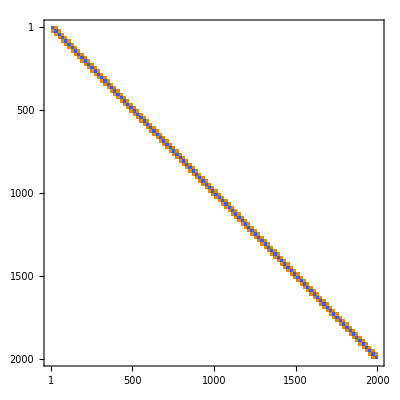

```mathematica
MatrixPlot[m]
```

```mathematica
Eigenvalues[m,2,Method->"Banded"]
```

{-4.,-3.99999}

### “FEAST”

The FEAST method can be used for real symmetric or complex Hermitian machine-precision matrices. The method is most useful for finding eigenvalues in a given interval.

The following suboptions can be specified for the method “FEAST”:

Compute eigenvalues in the interval {-1,-0.9}:

```mathematica
s=SparseArray[{{i_,i_}->-2.,{i_,j_}/;Abs[i-j]==1->1.},{1000,1000}];
```

Use “Interval” to specify the interval:

```mathematica
Eigenvalues[s,Method->{"FEAST","Interval"->{-1.0,-0.9}}]
```

{-0.996378,-0.990954,-0.985539,-0.980135,-0.97474,-0.969356,-0.963982,-0.958618,-0.953264,-0.947921,-0.942588,-0.937265,-0.931953,-0.926651,-0.92136,-0.916079,-0.91081,-0.905551,-0.900302}

### Quartics

A 4x4 matrix:

```mathematica
m=Table[{1,2,-1,-2}^j,{j,4}]
```

{{1,2,-1,-2},{1,4,1,4},{1,8,-1,-8},{1,16,1,16}}

In general, for a 4x4 matrix, the result will be given in terms of Root objects:

```mathematica
Eigenvalues[m]
```

{Root19.4Root[-288+240 #1-20 #1^3+#1^4&,4]19.401868691492574,Root-3.67Root[-288+240 #1-20 #1^3+#1^4&,1]-3.6683948675966267,Root2.84Root[-288+240 #1-20 #1^3+#1^4&,3]2.84345586743678,Root1.42Root[-288+240 #1-20 #1^3+#1^4&,2]1.4230703086672745}

You can get the result in terms of radicals using the Cubics and Quartics options:

```mathematica
Eigenvalues[m,Cubics->True,Quartics->True]
```

{5+√(25+(38 2^(2/3))/(-225+ⅈ √59119)^(1/3)+(2 (-225+ⅈ √59119))^(1/3))+1/2 √(200-(152 2^(2/3))/(-225+ⅈ √59119)^(1/3)-4 (2 (-225+ⅈ √59119))^(1/3)+760/(√(25+(38 2^(2/3))/(-225+ⅈ √59119)^(1/3)+(2 (-225+ⅈ √59119))^(1/3)))),5-√(25+(38 2^(2/3))/(-225+ⅈ √59119)^(1/3)+(2 (-225+ⅈ √59119))^(1/3))-1/2 √(200-(152 2^(2/3))/(-225+ⅈ √59119)^(1/3)-4 (2 (-225+ⅈ √59119))^(1/3)-760/(√(25+(38 2^(2/3))/(-225+ⅈ √59119)^(1/3)+(2 (-225+ⅈ √59119))^(1/3)))),5+√(25+(38 2^(2/3))/(-225+ⅈ √59119)^(1/3)+(2 (-225+ⅈ √59119))^(1/3))-1/2 √(200-(152 2^(2/3))/(-225+ⅈ √59119)^(1/3)-4 (2 (-225+ⅈ √59119))^(1/3)+760/(√(25+(38 2^(2/3))/(-225+ⅈ √59119)^(1/3)+(2 (-225+ⅈ √59119))^(1/3)))),5-√(25+(38 2^(2/3))/(-225+ⅈ √59119)^(1/3)+(2 (-225+ⅈ √59119))^(1/3))+1/2 √(200-(152 2^(2/3))/(-225+ⅈ √59119)^(1/3)-4 (2 (-225+ⅈ √59119))^(1/3)-760/(√(25+(38 2^(2/3))/(-225+ⅈ √59119)^(1/3)+(2 (-225+ⅈ √59119))^(1/3))))}

## Applications

Smallest eigenvalue of a Hilbert matrix:

```mathematica
Eigenvalues[HilbertMatrix[8],-1]
```

{Root1.11 × 10^-10Root[1-9052917760 #1+«9»+365356847125734485878112256000000 #1^8&,1]1.1115389663724424e-10}

```mathematica
N[Eigenvalues[HilbertMatrix[8],-1]]
```

{1.11154×10^-10}

## Properties & Relations